```mathematica
Clear["`*"]
```

```mathematica
img=-Graphics-;
{x,y}=ImageDimensions@img;
seed=SeedRandom@Hash@img
(*{个体总数,个体基因数,生育数,变异数,变异度,进化容错率}*)
{unit,gene,number,variate,var,error}={4,5,8,2,1.2,2};
婚配=RandomSample[Range[unit],unit];
子代=Flatten[Table[10Floor[(i-1)/(unit*gene)]+RandomSample[Range[2gene],2gene],{i,1,number*unit*gene/2}]];
(*定义域控制函数*)
if=Function[a,If[a>1,1,If[a<0,0,a]]];
IF=Function[{a,b},{If[a>x,x,If[a<0,0,a]],If[b>y,y,If[b<0,0,b]]}];
(*基因变异函数*)
Variation[l_]:={
if/@Cross[RandomReal[{-var,var},3],l[[1]]],
if@(RandomReal[{-var,var}]l[[2]]),
IF@@@Ceiling[l[[3]].RandomReal[{-var,var},{2,2}]]}
(*个体变异函数*)
Mutation[list_]:=Module[{change},
change=list[[1;;variate]];
change=Variation/@change;
Join[change,list[[variate+1;;-1]]]]
ToGraphics[{a_,b_,c_}]:={RGBColor[a],Opacity[b],Triangle[c]}
(*初始状态*)
颜色=RandomReal[1,{unit*gene,3}];
透明度=RandomReal[1,unit*gene];
坐标=Partition[Transpose@{RandomInteger[{0,x},3unit*gene],
RandomInteger[{0,y},3unit*gene]},3];
```

```mathematica
(*遗传进化开始!*)
幸存者=Partition[Transpose[{颜色,透明度,坐标}],gene];
Monitor[Do[家庭=Partition[Partition[Flatten[幸存者,1],gene][[婚配]],2];
后代=Mutation/@Partition[Flatten[家庭[[1]],1][[子代]],gene];
评分=ImageDistance[img,#]&/@(Graphics/@Map[ToGraphics,后代,{2}]);
适应度=Transpose@SortBy[Transpose@{Range[unit*number/2],评分},Last];
幸存者=后代[[Join[适应度[[1,1;;unit-error]],
RandomSample[适应度[[1,unit-error+1;;-1]],error]]]];
,{进化代数,4}],进化代数]
```

Part::partw: {{{0.803751,0.128985,0.0441466},0.0265043,{{12,136},{11,168},{131,165}}},«8»,{{0.739856,0.675798,0.900748},0.153372,{{106,115},{108,73},{144,6}}}} 的部分 {7,4,5,2,1,6,9,3,10,8,7,5,1,2,10,3,4,9,8,6,7,9,1,5,4,3,10,8,2,6,6,5,10,2,1,9,4,7,8,3,1,10,7,4,6,9,3,2,8,5,«750»} 不存在.

Part::argm: Part 使用 0 个参数调用；预计有 1 或更多参数.

Transpose::nmtx: {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]} 的前两层无法转置.

Part::take: 无法在 Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}] 中提取位置 1 至 2.

Part::take: 无法在 Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}] 中提取位置 3 至 -1.

RandomSample::lrwl: 进行采样的项目集合 Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,3;;-1⟧ 应该是一个非空列表或者一个规则 weights -> choices.

Join::heads: 位置 1 和 2 处的头部 Part 和 RandomSample 应该是一样的.

Part::pkspec1: 表达式 Join[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,1;;2⟧,RandomSample[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,3;;-1⟧,2]] 不能作为部分指定使用.

Part::partw: {} 的部分 {4,1,2,3} 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

Part::argm: Part 使用 0 个参数调用；预计有 1 或更多参数.

Transpose::nmtx: {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]} 的前两层无法转置.

General::stop: 在本次计算中，Transpose::nmtx 的进一步输出将被抑制.

Part::take: 无法在 Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}] 中提取位置 1 至 2.

General::stop: 在本次计算中，Part::take 的进一步输出将被抑制.

RandomSample::lrwl: 进行采样的项目集合 Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,3;;-1⟧ 应该是一个非空列表或者一个规则 weights -> choices.

Join::heads: 位置 1 和 2 处的头部 Part 和 RandomSample 应该是一样的.

Part::pkspec1: 表达式 Join[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,1;;2⟧,RandomSample[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,3;;-1⟧,2]] 不能作为部分指定使用.

Part::argm: Part 使用 0 个参数调用；预计有 1 或更多参数.

General::stop: 在本次计算中，Part::argm 的进一步输出将被抑制.

RandomSample::lrwl: 进行采样的项目集合 Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,3;;-1⟧ 应该是一个非空列表或者一个规则 weights -> choices.

General::stop: 在本次计算中，RandomSample::lrwl 的进一步输出将被抑制.

Join::heads: 位置 1 和 2 处的头部 Part 和 RandomSample 应该是一样的.

General::stop: 在本次计算中，Join::heads 的进一步输出将被抑制.

Part::pkspec1: 表达式 Join[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,1;;2⟧,RandomSample[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,3;;-1⟧,2]] 不能作为部分指定使用.

General::stop: 在本次计算中，Part::pkspec1 的进一步输出将被抑制.

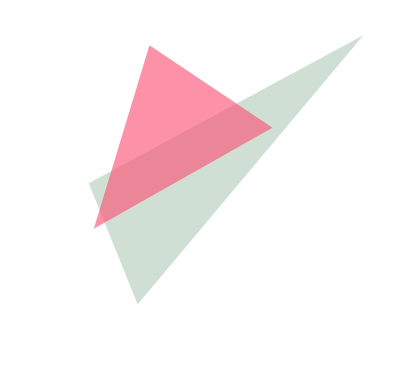
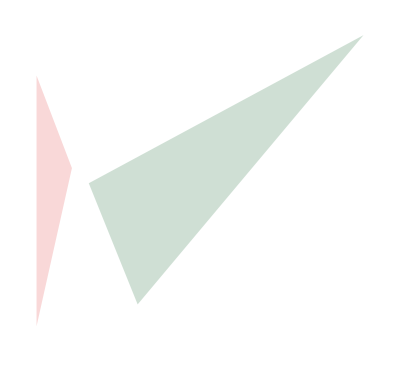
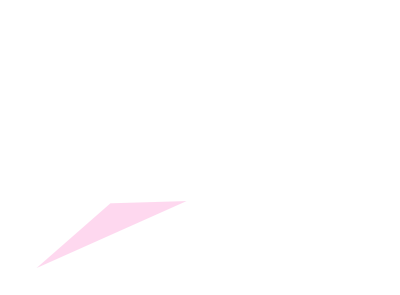
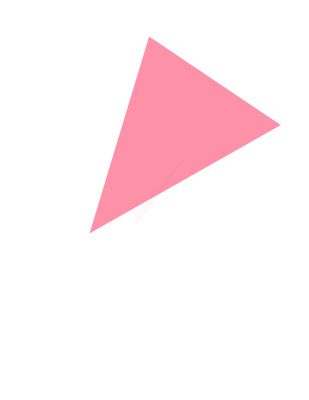

```mathematica
Graphics/@Map[ToGraphics,幸存者,{2}]
```

```mathematica
幸存者=Partition[Transpose[{颜色,透明度,坐标}],gene];
家庭=Partition[Partition[Flatten[幸存者,1],gene][[婚配]],2];
后代=Mutation/@Partition[Flatten[家庭,2][[子代]],gene];
评分=ImageDistance[img,#]&/@(Graphics/@Map[ToGraphics,后代,{2}])
适应度=Transpose@SortBy[Transpose@{Range[unit*number/2],评分},Last]
幸存者=后代[[Join[适应度[[1,1;;unit-error]],
RandomSample[适应度[[1,unit-error+1;;-1]],error]]]]
```

Part::partw: {{{0.803751,0.128985,0.0441466},0.0265043,{{12,136},{11,168},{131,165}}},«18»,{{0.689682,0.200886,0.14756},0.101511,{{174,16},{35,79},{162,174}}}} 的部分 {7,4,5,2,1,6,9,3,10,8,7,5,1,2,10,3,4,9,8,6,7,9,1,5,4,3,10,8,2,6,6,5,10,2,1,9,4,7,8,3,1,10,7,4,6,9,3,2,8,5,«750»} 不存在.

Part::argm: Part 使用 0 个参数调用；预计有 1 或更多参数.

Part[]

Transpose::nmtx: {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]} 的前两层无法转置.

Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]

Part::take: 无法在 Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}] 中提取位置 1 至 2.

Part::take: 无法在 Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}] 中提取位置 3 至 -1.

RandomSample::lrwl: 进行采样的项目集合 Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,3;;-1⟧ 应该是一个非空列表或者一个规则 weights -> choices.

Join::heads: 位置 1 和 2 处的头部 Part 和 RandomSample 应该是一样的.

Part::pkspec1: 表达式 Join[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,1;;2⟧,RandomSample[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,3;;-1⟧,2]] 不能作为部分指定使用.

Part[]⟦Join[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,1;;2⟧,RandomSample[Transpose[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Part[]}]]⟦1,3;;-1⟧,2]]⟧

```mathematica
幸存者=Partition[Transpose[{颜色,透明度,坐标}],gene];
家庭=Partition[Partition[Flatten[幸存者,1],gene][[婚配]],2];
后代=Mutation/@Partition[Flatten[家庭,2][[子代]],gene]
```

{{{{0,1,0},0.106322,{{142,0},{20,0},{120,0}}},{{0.00810316,0,0.238474},0.0192898,{{51,180},{0,84},{35,200}}},{{0.786913,0.327879,0.853931},0.64303,{{12,93},{100,20},{49,76}}},{{0.428342,0.332653,0.648712},0.358903,{{88,70},{189,159},{125,76}}},{{0.430261,0.3377,0.462574},0.5296,{{121,64},{41,9},{136,9}}}},318,{{{0.0523587,0,0},0.868973,{{200,149},{150,0},{164,0}}},3,{{0.218352,0.0405096,0.175134},20,{1}}}}
 |  |  |  |